```mathematica
SetDirectory[NotebookDirectory[]]
isoformRatios = Select[Import["isoform_ratio_table.tsv"], #[[2]] ≠ "NA"&]
```

/Users/verve/mr1

{{SRA run accession number,tissue,MR1:NM_001195000 normalized count,MR1:NM_001531 normalized count,NM_001531:NM_001195000 ratio},{SRR810619,Heart,28.1182,0,0},{SRR1433131,Blood Vessel,27.0468,0,0},{SRR660426,Skin,20.5036,0,0},{SRR662462,Skin,18.8588,0,0},{SRR658837,Skin,18.6104,0,0},{SRR659049,Nerve,18.3581,0,0},{SRR1340598,Ovary,18.2956,0,0},{SRR1360194,Colon,17.263,0,0},{SRR661373,Skin,15.1959,0,0},9383,{SRR1312428,Brain,5.16378,5.16378,0.5},{SRR658331,Heart,5.34632,5.34632,0.5},{SRR1315371,Brain,5.37934,5.37934,0.5},{SRR627449,Brain,5.52558,5.52558,0.5},{SRR1326292,Muscle,6.43383,6.43383,0.5},{SRR1076847,Blood,7.06841,7.06841,0.5},{SRR665393,Brain,7.68966,7.68966,0.5},{SRR662103,Adipose Tissue,7.9359,7.9359,0.5},{SRR663549,Lung,8.87566,8.87566,0.5},{SRR614455,Brain,8.9945,8.9945,0.5}}
 |  |  |  |

```mathematica
tissues = DeleteDuplicates[isoformRatios[[Range[2, Length[isoformRatios]]]][[All, 2]]]
```

{Heart,Blood Vessel,Skin,Nerve,Ovary,Colon,Adipose Tissue,Esophagus,Brain,Breast,Stomach,Small Intestine,Uterus,Muscle,Adrenal Gland,Pancreas,Liver,Bladder,Testis,Thyroid,Pituitary,Blood,Lung,Fallopian Tube,Prostate,Vagina,Salivary Gland,Kidney,Cervix Uteri,Spleen,Bone Marrow}

```mathematica
stratifiedIsoformRatios = Table[#[[5]]&/@Select[isoformRatios, #[[2]] == tissues[[i]] &], {i, 1, Length[tissues]}];
```

```mathematica
{sortedTissues, sortedStratifiedIsoformRatios} = Transpose[Sort[Transpose[{tissues, stratifiedIsoformRatios}], Median[#1[[2]]] < Median[#2[[2]]]&]];
```

```mathematica
chartLabelTransform = Rotate[#, 70 Degree]&
```

#1&

```mathematica
ColorData["ThermometerColors"][1]
```

RGBColor[0.534081, 0.0853132, 0.16669]

```mathematica
medians =Median/@sortedStratifiedIsoformRatios
```

{0.142857,0.147059,0.15,0.153846,0.15625,0.160715,0.160715,0.166666,0.166666,0.166667,0.166667,0.166667,0.168561,0.170455,0.171429,0.18,0.1875,0.190477,0.193549,0.200001,0.20924,0.20943,0.211782,0.214286,0.222223,0.227273,0.230769,0.234042,0.235486,0.255211,0.260563}

```mathematica
lowerBound = Min[medians]
```

0.142857

```mathematica
upperBound=Max[medians]
```

0.260563

```mathematica
customThermometer = ColorData["ThermometerColors"][(#-lowerBound)/(upperBound-lowerBound)]&
```

ColorData[ThermometerColors][(#1-lowerBound)/(upperBound-lowerBound)]&

```mathematica
legend=BarLegend[{customThermometer, {lowerBound-.01, upperBound}}, LegendLayout->"Row", LegendMargins->0]
```

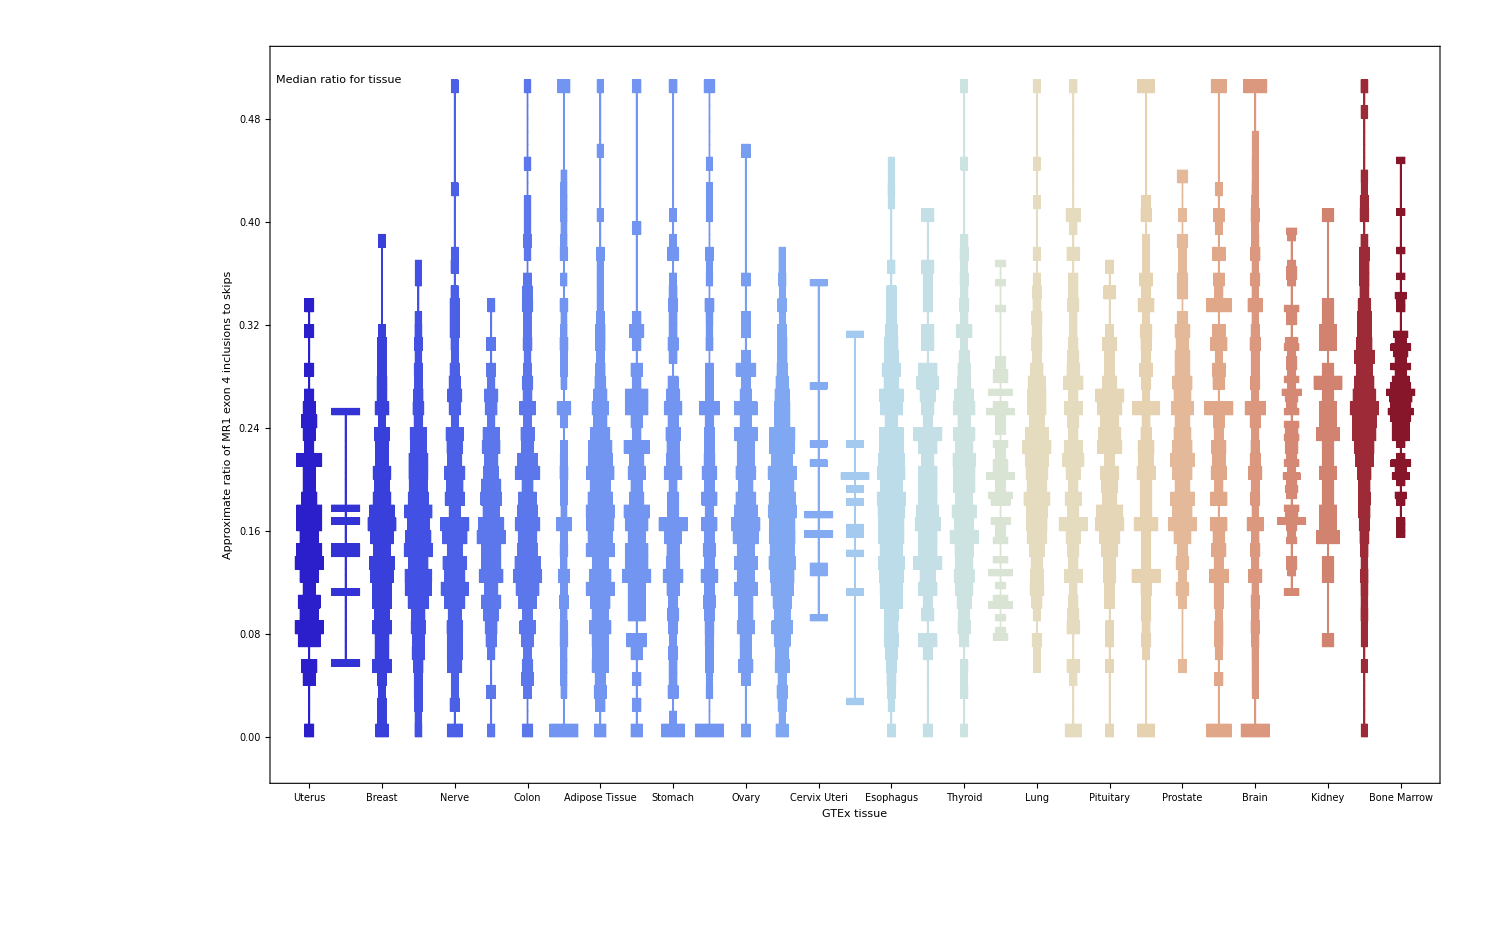

```mathematica
histogramDensityPlot = Show[Legended[DistributionChart[sortedStratifiedIsoformRatios, ChartLabels->chartLabelTransform/@sortedTissues, BarSpacing->.3, ChartElementFunction->(ChartElementDataFunction["HistogramDensity","Bins"->40]), BaseStyle->{FontName->"Helvetica", FontSize->20}, ImageSize->{1500, 1000}, Frame->True, FrameLabel->{"GTEx tissue","Approximate ratio of MR1 exon 4 inclusions to skips"}, ChartStyle->Table[ColorData["ThermometerColors"][(medians[[i]]-lowerBound)/(upperBound-lowerBound)], {i, 1, Length[medians]}]],Placed[legend, {.08,.96}]], Graphics[Style[Text["Median ratio for tissue", {1.8,.51}], FontFamily->"Helvetica", FontSize->12]]]
```

```mathematica
Export["histogramDensityPlot.pdf", histogramDensityPlot]
```

histogramDensityPlot.pdf